```mathematica
(* Computational Methods Lab 7 *) 

(*Data of Pendellum*)
b =1;
MOI = 9000; 
fD =  0.0;  
rCM = 15; 
mass = 30;
g = 9.81; 
w0 = 0; 
theta0 = 1.1; 
angularFrequency = 0.66;
t0 = 0; 
alpha0 = (-((rCM*mass*g*Sin[theta0])) - ((((rCM)^2)*b*w0)) + ( (rCM*fD*Sin[angularFrequency])*t0))/MOI;
wDrive=0; 
If[ fD ==0 && b ==0, omega2 = (rCM*mass*g/MOI)^0.5];
If[ fD ==0 && b  ≠ 0, omega2 = ((rCM*mass*g/MOI) - (((b*30^2)/(2*MOI))^2) )^0.5];
If[ fD  ≠ 0 , omega2 = angularFrequency];
omega2

(*Initial Conditions*)
w0 = 0;
t0 = 0; 
theta0 = 1; 
deltaT = 0.01; 
x0 = Sin[theta0];
Energy0 = 0.5MOI*w0^2 + mass*g*rCM*(1-Cos[theta0]); 


(*Starting Values*)
w = w0; 
theta= theta0;
alpha = alpha0; 
x = x0; 
Energy = Energy0;
TimeTest0 =2*Pi/omega2 ;
TimeTest=TimeTest0;
PeriodCounter = 1;
TimeTest
```

0.69857

8.99435

0

0.1

t

{{0.0892351,-0.00489885},{0.079693,-0.00491403},{0.0711094,-0.00524603},{0.0634834,-0.00516067},{0.0566136,-0.00532453},{0.0505228,-0.00515736},{0.0450282,-0.00519203},{0.0401676,-0.00496879},{0.0358258,-0.00473741},{0.0319015,-0.00465665},{0.0284413,-0.00440141},{0.0253095,-0.00427187},{0.0225547,-0.00400998},{0.0200579,-0.00385326},{0.0178671,-0.00359695},{0.0159128,-0.00335144},{0.0141381,-0.00318598},{0.0125862,-0.0029559},{0.0111748,-0.00279272},{0.00994376,-0.00258181},{0.00882251,-0.00242669},{0.00784706,-0.00223664}}

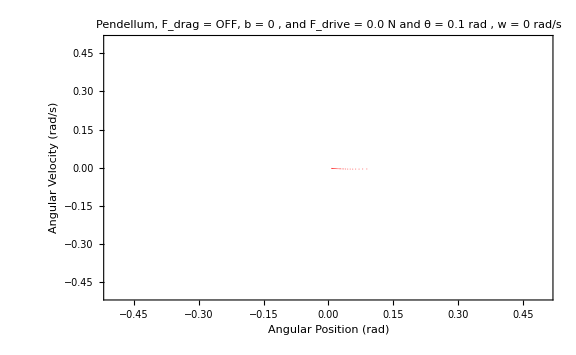

{{0.0892351,-0.00489885},{0.079693,-0.00491403},{0.0711094,-0.00524603},{0.0634834,-0.00516067},{0.0566136,-0.00532453},{0.0505228,-0.00515736},{0.0450282,-0.00519203},{0.0401676,-0.00496879},{0.0358258,-0.00473741},{0.0319015,-0.00465665},{0.0284413,-0.00440141},{0.0253095,-0.00427187},{0.0225547,-0.00400998},{0.0200579,-0.00385326},{0.0178671,-0.00359695},{0.0159128,-0.00335144},{0.0141381,-0.00318598},{0.0125862,-0.0029559},{0.0111748,-0.00279272},{0.00994376,-0.00258181},{0.00882251,-0.00242669},{0.00784706,-0.00223664}}

```mathematica
(*limits of iterations *) 
myData0= List[];
tmin = 0;
tmax = 200;

w = 0; 
theta= 0.1;
alpha = alpha0; 
x = x0; 
Energy = Energy0;
w
theta
t

myData0= List[];
Do [    wPlus = w + alpha*deltaT;
	thetaPlus = theta + wPlus*deltaT; 
Energy = (0.5*MOI*(w^2)) +(mass*g* rCM*(1-Cos[theta]));
w= wPlus;
theta = thetaPlus; 
x = Sin[theta];
If[theta>π,theta=theta-(2*π)];
If [theta < -π , theta = theta + (2*π)];
alpha = (-((rCM*mass*g*Sin[thetaPlus]))- (((rCM^2)*b*wPlus)) + ( (rCM*fD*Sin[angularFrequency*t])))/MOI;
If[( t> 0 && t<tmax ),
 If[t> TimeTest,
		         myData0 = Append[myData0,{theta,w}];
		         PeriodCounter = PeriodCounter + 1;
		         TimeTest = PeriodCounter*TimeTest0;
		       ]],
{t,tmin,tmax,deltaT}]; 
	
myData0
(*p4=ListLinePlot[{myData0}, PlotRange->All,ImageSize->Large,PlotStyle->{RGBColor[1,0,0],PointSize[0.002]},PlotLabel -> (" Pendellum,   F_drag = OFF, b = 0 , and  F_drive = 0 N and θ = 1.1 rad (purple), θ = 0.1 rad (blue)"), Joined->False,Frame->True,FrameLabel->{"Angular Position (rad)","Angular Velocity (rad/s)","",""},LabelStyle->(FontSize->14)]*)

ListPlot[myData0,PlotLabel -> (" Pendellum,   F_drag = OFF, b = 0 , and  F_drive = 0.0 N and θ = 0.1 rad , w = 0 rad/s"),PlotRange->{{-0.5,0.5},{-0.5,0.5}},ImageSize->Large, Joined->False,Frame->True,FrameLabel->{"Angular Position (rad)","Angular Velocity (rad/s)","",""},FrameLabel->{"x","v","",""},LabelStyle->(FontSize->14), PlotStyle->{RGBColor[1,0,0],PointSize[0.001]}]
myData0
```

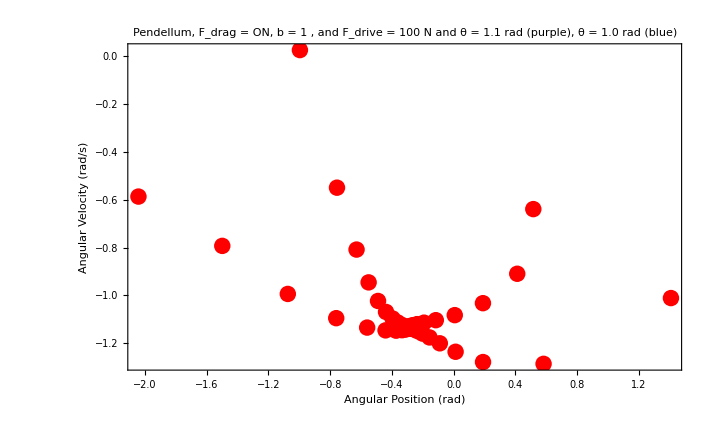

```mathematica
(*phasePlot2 = Drop[allData, None, {4,6}];
phasePlot2 = Drop[phasePlot2, None, {1,1}];

thetaTime = Drop[allData,None, {2,2}];
thetaTime = Drop[thetaTime,None, {3,3}];
thetaTime  = Drop[thetaTime, None,{3,3}];
thetaTime  = Drop[thetaTime, None,{3,3}];

xTime = Drop[allData, None, {2,4}];
xTime = Drop[xTime, None, {3,3}];

ETime = Drop[allData, None, {2,5}];

thetaTime
xTime
ETime
phasePlot2

p1=ListPlot[xTime,PlotRange-> All,Joined->True,Frame->True,ImageSize->Large,PlotLabel -> ("Simple Pendellum, no drag force and no driving force"),FrameLabel->{"t(s)","Displacement(m)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p2=ListPlot[ETime,PlotRange->All,Joined->True,Frame->True,ImageSize->Large,PlotLabel -> ("Simple Pendellum, no drag force and no driving force"),FrameLabel->{"t(s)","Total Energy(J)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p3=ListPlot[thetaTime,PlotRange->All,ImageSize->Large,PlotLabel -> ("Pendellum,   F_drag , b= 5, and  F_drive = 100 N"), Joined->True,Frame->True,FrameLabel->{"t(s)","Angular Position (rad)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p4=ListPlot[phasePlot2,PlotRange->All,ImageSize->Large,PlotLabel -> ("Simple Pendellum,   F_drag =0 , and  F_drive = 0 N , initial Angular Velocity = 2"), Joined->True,Frame->True,FrameLabel->{"Angular Position (rad)","Angular Velocity (rad/s)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]
p4=ListLinePlot[{phasePlot1, phasePlot0}](*, PlotRange->All,ImageSize->Large,PlotLabel -> ("Simple Pendellum,   F_drag =0 , and  F_drive = 0 N , initial Angular Velocity = 2"), Joined->True,Frame->True,FrameLabel->{"Angular Position (rad)","Angular Velocity (rad/s)","",""},LabelStyle->(FontSize->14),PlotStyle->RGBColor[1,0,0]]*) *)
```